```mathematica
$Assumptions = Im[r]==0&&Im[k]==0&&Im[α]==0&&Im[l]==0&&Im[R]==0&&Im[α]==0;
```

```mathematica
F[r_,k_,α_,l_,R_] := (k/R SphericalBesselJ[l,α] D[SphericalBesselJ[l,k],k]-α/R SphericalBesselJ[l,k] D[SphericalBesselJ[l,α],α])*(k/R SphericalBesselJ[l,α] D[SphericalBesselY[l,k],k]-α/R SphericalBesselY[l,k] D[SphericalBesselJ[l,α],α])^(-1);
```

```mathematica
F[r,kR,αR,0,R]//FullSimplify
```

(kR sin(αR) cot(kR)-αR cos(αR))/(kR sin(αR)+αR cos(αR) cot(kR))

```mathematica
F[r,k,α,0,R]//FullSimplify
```

(-α Cos[α]+k Cot[k] Sin[α])/(α Cos[α] Cot[k]+k Sin[α])

```mathematica
(k sin(α R) cot(k R)-α cos(α R))/(k sin(α R)+α cos(α R) cot(k R))
```

(-α Cos[R α]+k Cot[k R] Sin[R α])/(α Cos[R α] Cot[k R]+k Sin[R α])

```mathematica
((-α Cos[R α]+k Cot[k R] Sin[R α])/(α Cos[R α] Cot[k R]+k Sin[R α]))^-1*k//FullSimplify
```

(k (α Cos[R α] Cot[k R]+k Sin[R α]))/(-α Cos[R α]+k Cot[k R] Sin[R α])

```mathematica
Series[Sqrt[k^2+h],{k,0,6}]
```

√h+k^2/(2 √h)-k^4/(8 h^(3/2))+k^6/(16 h^(5/2))+O[k]^7

```mathematica
Series[Tan[Sqrt[k^2+ h] R],{k,0,5}]
```

```mathematica
α = Sqrt[k^2+h];
```

```mathematica
(k (α Cos[R α] Cot[k R]+k Sin[R α]))/(-α Cos[R α]+k Cot[k R] Sin[R α])
```

(k (√(h+k^2) Cos[√(h+k^2) R] Cot[k R]+k Sin[√(h+k^2) R]))/(-√(h+k^2) Cos[√(h+k^2) R]+k Cot[k R] Sin[√(h+k^2) R])

```mathematica
Series[(k (α Cos[R α] Cot[k R]+k Sin[R α]))/(-α Cos[R α]+k Cot[k R] Sin[R α]),{k,0,2}]//FullSimplify
```

1/((tan(√h R))/(√h)-R)+(k^2 (h^(3/2) R^3+(3/2-3 h R^2) sin(2 √h R)+√h R (h R^2-3) cos(2 √h R)))/(6 √h (sin(√h R)-√h R cos(√h R))^2)+O(k^3)

```mathematica
Series[(k (α Cos[R α] Cot[k R]+k Sin[R α]))/(-α Cos[R α]+k Cot[k R] Sin[R α]),{k,0,2}]
```

-(√h Cos[√h R])/(√h R Cos[√h R]-Sin[√h R])+((-3 √h R Cos[√h R]^2+2 h^(3/2) R^3 Cos[√h R]^2+3 Cos[√h R] Sin[√h R]-6 h R^2 Cos[√h R] Sin[√h R]+3 √h R Sin[√h R]^2) k^2)/(6 √h (√h R Cos[√h R]-Sin[√h R])^2)+O[k]^3

```mathematica
Series[(k (α Cos[R α] Cot[k R]+k Sin[R α]))/(-α Cos[R α]+k Cot[k R] Sin[R α]),{k,0,2}]//FullSimplify
```

```mathematica
Plot[Tan[x]/x-1,{x,0,10},AxesLabel->{"β","a_s/R(β)"}]
```

```mathematica
Plot[Tan[x]/x-1,{x,-5,5},AxesLabel->{"β","a_s/R(β)"}]
```

```mathematica
f1[b_]:=(b^2+(3/2-3b^2)Sin[2b]+b(b^2-3)Cos[2b])/(3b(Sin[b]-b Cos[b])^2);
```

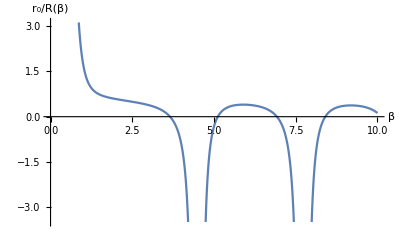

```mathematica
Plot[f1[x],{x,0,10},AxesLabel->{"β","r_0/R(β)"}]
```

```mathematica
f2[x_] := ((Sin[x]-x Cos[x])/x^3)^2;
```

```mathematica
f3[α_]:= NIntegrate[Sin[θ]*f2[2α Sin[θ/2]],{θ,0,Pi}];
```

```mathematica
f3[0.01]
```

0.39503

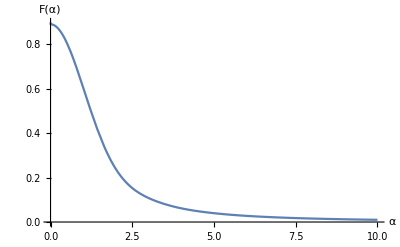

```mathematica
Plot[f3[x],{x,0,10},AxesLabel->{"α","F(α)"}]
```

```mathematica
N[16*Pi/9/(8 Pi)]
```

0.222222

```mathematica
N[16*Pi/9]
```

5.58505

```mathematica
8*Pi*.2222
```

5.5845

```mathematica
f2[x]
```

(4 (-x Cos[x]+Sin[x])^2)/x^6

```mathematica
Clear[α]
```

```mathematica
(Sin[ArcTan[x]])^2
```

x^2/(1+x^2)

```mathematica
f2[2Sin[θ/2]]
```

1/16 Csc[θ/2]^6 (-2 Cos[2 Sin[θ/2]] Sin[θ/2]+Sin[2 Sin[θ/2]])^2

```mathematica
Table[(2l+1)/2 NIntegrate[f2[2 1 Sin[θ/2]] LegendreP[l,Cos[θ]] Sin[θ],{θ,0,Pi}],{l,0,2,1}]
```

{0.301862,0.126507,0.0151107}

```mathematica
f4[α_,l_]:=(2l+1/2)*NIntegrate[f2[2 α Sin[θ/2]] LegendreP[l,Cos[θ]] Sin[θ],{θ,0,Pi}];
```

```mathematica
f4[1,1]
```

0.210846

```mathematica
ListPlot[f4[1,l],{l,0,3,1}]
```

```mathematica
f5[α_,l_]:=(2l+1)/2 NIntegrate[f6[2 α Sin[θ/2]] LegendreP[l,Cos[θ]] Sin[θ],{θ,0,Pi}];
```

```mathematica
f5[1,4]
```

{0.301862,0.126507,0.0151107,0.000928228,0.0000354509}

```mathematica
Plot[f5[α,5],{α,0.1,1}]
```

$Aborted

```mathematica
f5[7,4]
```

{0.0101528,0.0286385,0.0432799,0.053203,0.0580416}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.368107}. NIntegrate obtained 2.64795×10^-10 and 2.89457×10^-16 for the integral and error estimates.

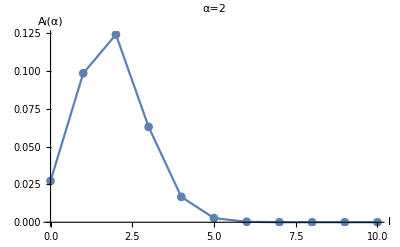

```mathematica
ListPlot[Table[{l,f5[4,l]},{l,0,10}],Joined->True,PlotMarkers->Automatic,
AxesLabel->{"l","A_l(α)"},PlotLabel->"α=1"]
```

```mathematica
Table[{{l,f5[5,l]}},{l,0,10}]
```

```mathematica
Table[{i,i+1},{i,0,3}]
```

{{0,1},{1,2},{2,3},{3,4}}

```mathematica
f6[x_] := ((Sin[x]-x Cos[x])/x^3);
```

```mathematica
f7[α_,n_]:=ListPlot[Table[{l,f5[α,l]},{l,0,n}],Joined->True,PlotMarkers->Automatic,
AxesLabel->{"l","A_l(α)"},PlotLabel->StringJoin["α=",ToString[α]],PlotRange->All]
```

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

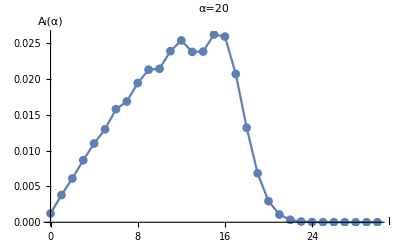

```mathematica
f7[20,30]
```

```mathematica
Integrate[Exp[-x^2/(a^2)],{x,-∞,∞}]
```

ConditionalExpression[(√π)/(√(1/a^2)),Re[a^2]>0]